```mathematica
D2[n_, k_, s_] := D2[n,k,s]=Sum[ j^-s D2[Floor[n/j],k-1,s],{j,2,n}];D2[n_,0,s_]:=1
bins[ z_, a_] := Product[ (z-k),{k,0,a-1}]/a!
DD[n_,z_,s_]:=Expand[Sum[bins[z,a] D2[n,a,s],{a,0,Log[2,n]}]]
```

```mathematica
N[Limit[D[(DD[100,z,s]-1)/z,{s,8}]/.s->0,z->0]]
```

1.47956×10^6

```mathematica
ll[n_,t_]:=Limit[ (DD[n,z,0]-1)/z,z->0]+N[Sum[ t^k / k! Limit[D[(DD[n,z,s]-1)/z,{s,k}]/.s->0,z->0],{k,1,16}]]
```

```mathematica
ll[100,-1]
```

1156.48

```mathematica
1
```

```mathematica
N[Limit[ (DD[100,z,-1]-1)/z,z->0]]
```

1156.48

```mathematica
l1[n_,t_]:= DD[n,1,0]+N[Sum[ t^k / k! D[(DD[n,1,s]),{s,k}]/.s->0,{k,1,48}]]
```

```mathematica
l1[100,t]
```

100-363.739 t+704.165 t^2-937.029 t^3+954.512 t^4-789.543 t^5+550.514 t^6-332.037 t^7+176.549 t^8-83.9678 t^9+36.134 t^10-14.201 t^11+5.13657 t^12-1.72104 t^13+0.537133 t^14-0.156899 t^15+0.0430744 t^16-0.0111551 t^17+0.00273403 t^18-0.000636014 t^19+0.0001408 t^20-0.0000297332 t^21+6.00224×10^-6 t^22-1.16057×10^-6 t^23+2.15323×10^-7 t^24-3.83967×10^-8 t^25+6.59084×10^-9 t^26-1.09055×10^-9 t^27+1.74169×10^-10 t^28-2.68814×10^-11 t^29+4.01403×10^-12 t^30-5.80522×10^-13 t^31+8.13951×10^-14 t^32-1.10746×10^-14 t^33+1.46348×10^-15 t^34-1.87992×10^-16 t^35+2.34923×10^-17 t^36-2.85803×10^-18 t^37+3.38742×10^-19 t^38-3.91401×10^-20 t^39+4.41164×10^-21 t^40-4.85362×10^-22 t^41+5.21516×10^-23 t^42-5.47577×10^-24 t^43+5.62113×10^-25 t^44-5.64444×10^-26 t^45+5.54682×10^-27 t^46-5.33693×10^-28 t^47+5.02983×10^-29 t^48

```mathematica
(List@@NRoots[ l1[100,x]==0,x][[All,2]])
```

{-7.55469-3.52856 ⅈ,-7.55469+3.52856 ⅈ,-5.7879-4.16192 ⅈ,-5.7879+4.16192 ⅈ,-4.52745-4.47878 ⅈ,-4.52745+4.47878 ⅈ,-3.51819-4.63165 ⅈ,-3.51819+4.63165 ⅈ,-2.66855-4.68076 ⅈ,-2.66855+4.68076 ⅈ,-1.93343-4.65728 ⅈ,-1.93343+4.65728 ⅈ,-1.28672-4.57985 ⅈ,-1.28672+4.57985 ⅈ,-0.711766-4.46068 ⅈ,-0.711766+4.46068 ⅈ,-0.196773-4.30889 ⅈ,-0.196773+4.30889 ⅈ,0.272047-4.12977 ⅈ,0.272047+4.12977 ⅈ,0.715356-3.87949 ⅈ,0.715356+3.87949 ⅈ,0.852106-3.71314 ⅈ,0.852106+3.71314 ⅈ,0.906216-2.45483 ⅈ,0.906216+2.45483 ⅈ,0.974373-1.21578 ⅈ,0.974373+1.21578 ⅈ,1.34332-3.71213 ⅈ,1.34332+3.71213 ⅈ,1.8183-3.52108 ⅈ,1.8183+3.52108 ⅈ,2.26188-3.26388 ⅈ,2.26188+3.26388 ⅈ,2.6682-2.95038 ⅈ,2.6682+2.95038 ⅈ,3.03016-2.58663 ⅈ,3.03016+2.58663 ⅈ,3.34159-2.17892 ⅈ,3.34159+2.17892 ⅈ,3.59726-1.73425 ⅈ,3.59726+1.73425 ⅈ,3.79289-1.26017 ⅈ,3.79289+1.26017 ⅈ,3.92517-0.764739 ⅈ,3.92517+0.764739 ⅈ,3.99187-0.25636 ⅈ,3.99187+0.25636 ⅈ}

```mathematica
l1a[n_,t_,m_]:= DD[n,1,0]+N[Sum[ t^k / k! D[(DD[n,1,s]),{s,k}]/.s->0,{k,1,m}]]
```

```mathematica
(List@@NRoots[ l1a[100,x,50]==0,x][[All,2]])
```

{-7.93002-3.61438 ⅈ,-7.93002+3.61438 ⅈ,-6.12639-4.27727 ⅈ,-6.12639+4.27727 ⅈ,-4.83788-4.61665 ⅈ,-4.83788+4.61665 ⅈ,-3.80461-4.78825 ⅈ,-3.80461+4.78825 ⅈ,-2.93332-4.85358 ⅈ,-2.93332+4.85358 ⅈ,-2.17807-4.8445 ⅈ,-2.17807+4.8445 ⅈ,-1.51226-4.78002 ⅈ,-1.51226+4.78002 ⅈ,-0.9189-4.67257 ⅈ,-0.9189+4.67257 ⅈ,-0.386556-4.53108 ⅈ,-0.386556+4.53108 ⅈ,0.0945205-4.36426 ⅈ,0.0945205+4.36426 ⅈ,0.548861-4.17545 ⅈ,0.548861+4.17545 ⅈ,0.807763-3.72871 ⅈ,0.807763+3.72871 ⅈ,0.906216-2.45483 ⅈ,0.906216+2.45483 ⅈ,0.974373-1.21578 ⅈ,0.974373+1.21578 ⅈ,1.07501-3.96142 ⅈ,1.07501+3.96142 ⅈ,1.58506-3.80414 ⅈ,1.58506+3.80414 ⅈ,2.05064-3.58588 ⅈ,2.05064+3.58588 ⅈ,2.4836-3.30966 ⅈ,2.4836+3.30966 ⅈ,2.87839-2.98122 ⅈ,2.87839+2.98122 ⅈ,3.2289-2.60604 ⅈ,3.2289+2.60604 ⅈ,3.52969-2.19009 ⅈ,3.52969+2.19009 ⅈ,3.77611-1.73991 ⅈ,3.77611+1.73991 ⅈ,3.96435-1.26256 ⅈ,3.96435+1.26256 ⅈ,4.0915-0.765506 ⅈ,4.0915+0.765506 ⅈ,4.15556-0.256503 ⅈ,4.15556+0.256503 ⅈ}

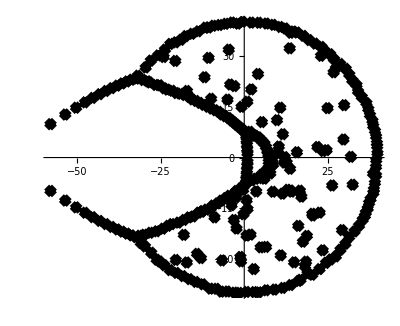

```mathematica
RootLocusPlot[1/Expand[l1a[100,x,300]],{k,0,1},FeedbackType->None]
```

```mathematica
l1b[n_,t_]:= DD[n,1,0]+N[Sum[ t^k / k! D[(DD[n,1,s]),{s,k}]/.s->0,{k,1,Infinity}]]
```

```mathematica
l1c[n_,t_,m_]:= DD[n,1,0]+Sum[ t^k / k! D[(DD[n,1,s]),{s,k}]/.s->0,{k,1,m}]
```

```mathematica
RootLocusPlot[1/Expand[l1c[100,x,300]],{k,0,1},FeedbackType->None]
```